# Calculus 2 Final Review

## Problem 1:

```mathematica
(* Sketch the region determined by the set of curves. Set up an integral to determine the area of the region. Evaluate the integral *)
```

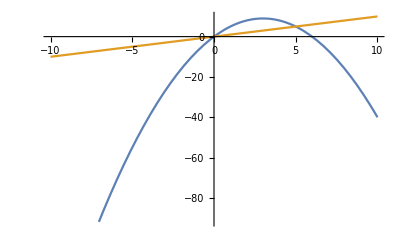

```mathematica
F[x_]:=6x-x^2;
G[x_]:=x;

Plot[{F[x],G[x]},{x,-10,10}]
```

```mathematica
Solve[G[x]==F[x],x]
```

{{x→0},{x→5}}

```mathematica
∫_-5^5 ((F[x])^2-(G[x])^2)ⅆx
```

```mathematica
125/6
```

## Problem 2:

```mathematica
ClearAll["Global`*"]
```

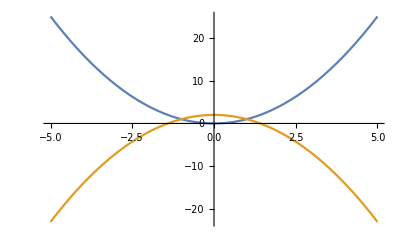

```mathematica
F[y_]:=y^2;
G[y_]:=2-y^2;

Plot[{F[y],G[y]},{y,-5,5}]
```

```mathematica
Show[%38,AxesLabel->{HoldForm[y-axis],HoldForm[x-axis]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

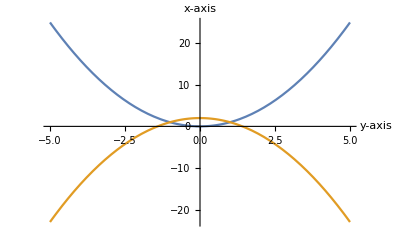
```mathematica
Rotate[-Graphics-,3 π/2]
```

-Graphics-

```mathematica
Solve[F[y]==G[y],y]
```

{{y→-1},{y→1}}

```mathematica
∫_-1^1 ((G[x])^2-(F[x])^2)ⅆx
```

16/3

## Problem 3

```mathematica
(*Sketch the region bounded by the lines and Curves. Set the an integral to determine the volume of the solid formed by rotatinf the region about the indicated axis

Evaluate the integral, make sure you can do both the Shell and Cylinder Method.*)
```

```mathematica
V==2π∫_a^b xf(x)ⅆx
```

```mathematica
V==π∫_a^b ((f(x))^2-(g(x))^2)ⅆx
```

```mathematica
ClearAll["Global`*"]
```

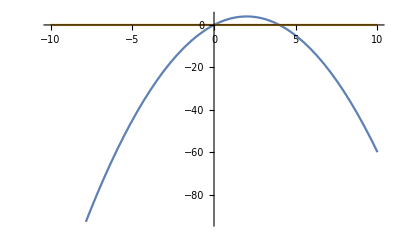

```mathematica
F[x_]:=-x^2+4x;
G[x_]:= 0;
Plot[{F[x],G[x]},{x,-10,10}]
```

```mathematica
Solve[F[x]==0,x]
```

{{x→0},{x→4}}

```mathematica
V==π∫_a^b ((f(x))^2-(g(x))^2)ⅆx
```

```mathematica
π∫_0^4 ((F[x])^2-(G[x])^2)ⅆx
```

(512 π)/15

## Problem 4

```mathematica
ClearAll["Global`*"]
```

```mathematica
x=2;
x+y=1; -> y=1-x;
y=x+1;

(*Set equations equal*)
x =0
```

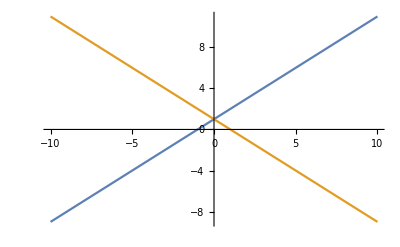

```mathematica
Plot[{y=x+1,y=1-x},{x,-10,10}]
```

```mathematica
2*π*∫_0^2 ((x+1)^2-(1-x)^2)ⅆx
```

16 π

## Problem 5:

```mathematica
ClearAll["Global`*"]
```

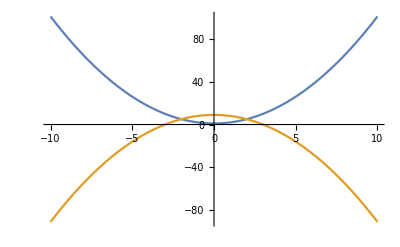

```mathematica
Plot[{x^2+1,9-x^2},{x,-10,10}]
```

```mathematica
Solve[x^2+1==9-x^2,x]
```

{{x→-2},{x→2}}

```mathematica
2^2+1
```

5

```mathematica
(*-2,5 and 2,5*)
```

```mathematica
2*π*∫_-2^2 ((9-x^2)^2-(x^2+1)^2)ⅆx
```

(1280 π)/3

## Problem 7: